### Start choosing the example:

```mathematica
t=17;
beta = 0;
A = 0.2;
Get["/Users/ribeirrd/eclipse-workspace/MFGraphs/MFGraphs/Examples/ExamplesParameters.m"];
g[x]
```

Get::noopen: Cannot open /Users/ribeirrd/eclipse-workspace/MFGraphs/MFGraphs/Examples/ExamplesParameters.m.

Log[x]

```mathematica
Get["/Users/ribeirrd/eclipse-workspace/MFGraphs/MFGraphs/MFGraphs.m"];
```

### DataToEquations and the critical congestion solver

```mathematica
Data=DataG[t]
```

```mathematica
Get["/Users/ribeirrd/eclipse-workspace/MFGraphs/MFGraphs/D2E2.m"];Data=<|"Vertices List"->{1,2,3},"Adjacency Matrix"->{{0,1,0},{0,0,1},{0,0,0}},"Entrance Vertices and Currents"->{{2,I1}},"Exit Vertices and Terminal Costs"->{{1,U1},{3,U2}},"Switching Costs"->{{1,2,3,S1},{3,2,1,S2}}|>;
CriticalCongestionSolver[d2e = Data2Equations[Data/.{I1->10,U1->0,U2->3,S1->1,S2->1}]]//AbsoluteTiming
```

inedges: {en2->2}

entry: {{2,en2->2}}

{{2,en2->2}}{{en2,en2->2}}

zerorun: {{2,en2->2},{ex1,1->ex1},{ex3,3->ex3}}

<|{1,1->2,1->ex1}→0,{1,1->ex1,1->2}→10000000000,{2,1->2,2->3}→1,{2,1->2,en2->2}→10000000000,{2,2->3,1->2}→1,{2,2->3,en2->2}→10000000000,{2,en2->2,1->2}→0,{2,en2->2,2->3}→0,{3,2->3,3->ex3}→0,{3,3->ex3,2->3}→10000000000|>

tripleclean done!

Preprocessing done!

{0.057707,<|j10→10,j9→0,j3→0,j7→0,j2→0,j4→13/2,j1→13/2,j6→7/2,j5→0,j8→7/2,u4→0,u8→3,jt10→0,jt2→0,jt4→0,jt6→0,jt7→13/2,jt8→7/2,jt9→7/2,u3→0,u7→3,u9→13/2,jt3→0,jt5→0,u2→13/2,u6→3,jt1→13/2,u1→0,u10→13/2,u5→13/2|>}

```mathematica
InEdges = {en2->2};
AllTransitions = {{1,1->2,1->ex1},{1,1->ex1,1->2},{2,1->2,2->3},{2,1->2,en2->2},{2,2->3,1->2},{2,2->3,en2->2},{2,en2->2,1->2},{2,en2->2,2->3},{3,2->3,3->ex3},{3,3->ex3,2->3}};
```

```mathematica
casesIn = {Last[#],__,#}&/@InEdges
Cases[AllTransitions,#]&/@casesIn //Flatten[#,1]&
```

{{2,__,en2->2}}

{{2,1->2,en2->2},{2,2->3,en2->2}}

```mathematica
casesOut = {First[#],#,__}&/@{1->ex1,3->ex3}
Cases[{{1,1->2,1->ex1},{1,1->ex1,1->2},{2,1->2,2->3},{2,1->2,en2->2},{2,2->3,1->2},{2,2->3,en2->2},{2,en2->2,1->2},{2,en2->2,2->3},{3,2->3,3->ex3},{3,3->ex3,2->3}},#]&/@casesOut
```

{{1,1->ex1,__},{3,3->ex3,__}}

{{{1,1->ex1,1->2}},{{3,3->ex3,2->3}}}

```mathematica
Cases[AllTransitions,#]&/@Join[casesIn,casesOut] //Flatten[#,1]&
```

{{2,1->2,en2->2},{2,2->3,en2->2},{1,1->ex1,1->2},{3,3->ex3,2->3}}

```mathematica
Last[en2->2]
```

2

```mathematica
BG=d2e["BG"];
```

```mathematica
MapThread
```

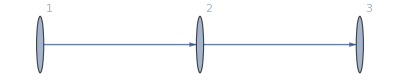
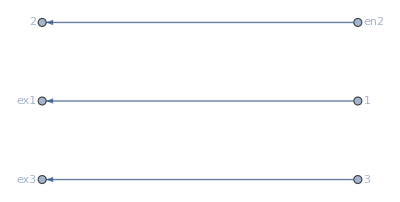
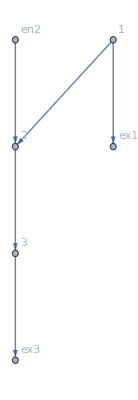
<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{0,0,0}},Entrance Vertices and Currents→{{2,10}},Exit Vertices and Terminal Costs→{{1,0},{3,3}},Switching Costs→{{1,2,3,0},{3,2,1,0}},VL→{1,2,3},AM→{{0,1,0},{0,0,1},{0,0,0}},EVC→{{2,10}},EVTC→{{1,0},{3,3}},SC→{{1,2,3,0},{3,2,1,0}},BG→-Graphics-,EntranceVertices→{2},InwardVertices→<|2→en2|>,ExitVertices→{1,3},OutwardVertices→<|1→ex1,3→ex3|>,InEdges→{en2->2},OutEdges→{1->ex1,3->ex3},AuxiliaryGraph→-Graphics-,FG→-Graphics-,EL→{1->2,1->ex1,2->3,3->ex3,en2->2},BEL→{1->2,2->3},FVL→{1,2,3,en2,ex1,ex3},jargs→{{1,1->2},{2,1->2},{1,1->ex1},{ex1,1->ex1},{2,2->3},{3,2->3},{3,3->ex3},{ex3,3->ex3},{en2,en2->2},{2,en2->2}},uargs→{{1,1->2},{2,1->2},{1,1->ex1},{ex1,1->ex1},{2,2->3},{3,2->3},{3,3->ex3},{ex3,3->ex3},{en2,en2->2},{2,en2->2}},AllTransitions→{{1,1->2,1->ex1},{1,1->ex1,1->2},{2,1->2,2->3},{2,1->2,en2->2},{2,2->3,1->2},{2,2->3,en2->2},{2,en2->2,1->2},{2,en2->2,2->3},{3,2->3,3->ex3},{3,3->ex3,2->3}},EntryArgs→{{2,en2->2}},EntryDataAssociation→<|{2,en2->2}→10|>,ExitCosts→<|ex1→0,ex3→3|>,js→{j1,j2,j3,j4,j5,j6,j7,j8,j9,j10},jvars→<|{1,1->2}→j1,{2,1->2}→j2,{1,1->ex1}→j3,{ex1,1->ex1}→j4,{2,2->3}→j5,{3,2->3}→j6,{3,3->ex3}→j7,{ex3,3->ex3}→j8,{en2,en2->2}→j9,{2,en2->2}→j10|>,us→{u1,u2,u3,u4,u5,u6,u7,u8,u9,u10},uvars→<|{1,1->2}→u1,{2,1->2}→u2,{1,1->ex1}→u3,{ex1,1->ex1}→u4,{2,2->3}→u5,{3,2->3}→u6,{3,3->ex3}→u7,{ex3,3->ex3}→u8,{en2,en2->2}→u9,{2,en2->2}→u10|>,jts→{jt1,jt2,jt3,jt4,jt5,jt6,jt7,jt8,jt9,jt10},jtvars→<|{1,1->2,1->ex1}→jt1,{1,1->ex1,1->2}→jt2,{2,1->2,2->3}→jt3,{2,1->2,en2->2}→jt4,{2,2->3,1->2}→jt5,{2,2->3,en2->2}→jt6,{2,en2->2,1->2}→jt7,{2,en2->2,2->3}→jt8,{3,2->3,3->ex3}→jt9,{3,3->ex3,2->3}→jt10|>,SignedCurrents→<|1->2→-j1+j2,2->3→-j5+j6|>,SwitchingCosts→<|{1,1->2,1->ex1}→0,{1,1->ex1,1->2}→0,{2,1->2,2->3}→0,{2,1->2,en2->2}→0,{2,2->3,1->2}→0,{2,2->3,en2->2}→0,{2,en2->2,1->2}→0,{2,en2->2,2->3}→0,{3,2->3,3->ex3}→0,{3,3->ex3,2->3}→0|>,EqPosJs→j1≥0&&j2≥0&&j3≥0&&j4≥0&&j5≥0&&j6≥0&&j7≥0&&j8≥0&&j9≥0&&j10≥0,EqPosJts→jt1≥0&&jt2≥0&&jt3≥0&&jt4≥0&&jt5≥0&&jt6≥0&&jt7≥0&&jt8≥0&&jt9≥0&&jt10≥0,EqCurrentCompCon→(j1==0||j2==0)&&(j3==0||j4==0)&&(j5==0||j6==0)&&(j7==0||j8==0)&&(j9==0||j10==0),EqTransitionCompCon→(jt1==0||jt2==0)&&(jt10==0||jt9==0)&&(jt3==0||jt5==0)&&(jt4==0||jt7==0)&&(jt6==0||jt8==0),NoDeadEnds→{{1,1->2},{1,1->ex1},{2,1->2},{2,2->3},{2,en2->2},{3,2->3},{3,3->ex3}},EqBalanceSplittingCurrents→j1==jt1&&j3==jt2&&j2==jt3+jt4&&j5==jt5+jt6&&j10==jt7+jt8&&j6==jt9&&j7==jt10,BalanceSplittingCurrents→{j1-jt1,j3-jt2,j2-jt3-jt4,j5-jt5-jt6,j10-jt7-jt8,j6-jt9,j7-jt10},NoDeadStarts→{{2,1->2},{ex1,1->ex1},{1,1->2},{3,2->3},{en2,en2->2},{2,2->3},{ex3,3->ex3}},RuleBalanceGatheringCurrents→<|j2→jt2,j4→jt1,j1→jt5+jt7,j6→jt3+jt8,j9→jt4+jt6,j5→jt10,j8→jt9|>,BalanceGatheringCurrents→{-j2+jt2,-j4+jt1,-j1+jt5+jt7,-j6+jt3+jt8,-j9+jt4+jt6,-j5+jt10,-j8+jt9},EqBalanceGatheringCurrents→j2==jt2&&j4==jt1&&j1==jt5+jt7&&j6==jt3+jt8&&j9==jt4+jt6&&j5==jt10&&j8==jt9,EqEntryIn→{j10==10},RuleEntryOut→<|j9→0|>,RuleExitCurrentsIn→<|j3→0,j7→0|>,RuleExitValues→<|u4→0,u8→3|>,EqValueAuxiliaryEdges→u9==u10&&u3==u4&&u7==u8,OutRules→{{1,1->ex1,1->2}→∞,{1,1->ex1,1->ex1}→∞,{1,1->ex1,2->3}→∞,{1,1->ex1,3->ex3}→∞,{1,1->ex1,en2->2}→∞,{3,3->ex3,1->2}→∞,{3,3->ex3,1->ex1}→∞,{3,3->ex3,2->3}→∞,{3,3->ex3,3->ex3}→∞,{3,3->ex3,en2->2}→∞},InRules→{{2,1->2,en2->2}→∞,{2,2->3,en2->2}→∞,{2,en2->2,en2->2}→∞},EqSwitchingByVertex→{u1≤u3&&u3≤u1,u2≤u5&&u2≤u10&&u5≤u2&&u5≤u10&&u10≤u2&&u10≤u5,u6≤u7&&u7≤u6},EqCompCon→(jt1==0||-u1+u3==0)&&(jt2==0||u1-u3==0)&&(jt3==0||-u2+u5==0)&&(jt4==0||u10-u2==0)&&(jt5==0||u2-u5==0)&&(jt6==0||u10-u5==0)&&(jt7==0||-u10+u2==0)&&(jt8==0||-u10+u5==0)&&(jt9==0||-u6+u7==0)&&(jt10==0||u6-u7==0),Nlhs→{-j1+j2-u1+u2,-j5+j6-u5+u6}|>

```mathematica
d2e
```

```mathematica
MFGEquations=DataToEquations[Data/.{I1->1,U1->0,U2->3,S1->1,S2->0}];//Timing
MFGEquations["uvars"]/.MFGEquations["criticalreduced1"][[2]]//KeySort
```

DataToEquations: Finished assembling strucural equations. Reducing the structural system ...

DataToEquations: Critical case ...

DataToEquations: The system is:
NonNegative[j90]&&NonNegative[1-j90]&&NonNegative[1-j90]&&NonNegative[j90]&&NonNegative[j90]&&NonNegative[j90]&&NonNegative[1-j90]&&NonNegative[1-j90]&&NonNegative[-u109]&&NonNegative[1-j90-u109+u111]&&NonNegative[j90+u109-u111]&&NonNegative[j90+u109-u113]&&NonNegative[u111-u113]&&NonNegative[4-j90-u111]&&(j90==0||-u109==0)&&(j90==0||j90+u109-u113==0)&&(1-j90==0||u111-u113==0)&&(1-j90==0||4-j90-u111==0)
and the rules are:
<|j93→1,u115→0,u117→3,j89→0,j91→1-j90,j92→1-j90,j94→j90,j95→0,j96→0,j97→0,j98→0,jt100→0,jt101→0,jt102→0,jt103→0,jt104→0,jt105→j90,jt106→1-j90,jt107→1-j90,jt108→0,jt99→j90,u110→0,u112→3,u114→j90+u109,u116→-1+j90+u111,u118→u113|>

DataToEquations: The system is:
j90==1&&u109==0&&u111==1&&u113==1
and the rules are:
<|j93→1,u115→0,u117→3,j89→0,j91→1-j90,j92→1-j90,j94→j90,j95→0,j96→0,j97→0,j98→0,jt100→0,jt101→0,jt102→0,jt103→0,jt104→0,jt105→j90,jt106→1-j90,jt107→1-j90,jt108→0,jt99→j90,u110→0,u112→3,u114→j90+u109,u116→-1+j90+u111,u118→u113|>

DataToEquations: It took 0.034572 seconds to reduce with NewReduce!

DataToEquations: Critical congestion solved.

DataToEquations: Done.

{0.057104,Null}

<|{1,1->2}→0,{1,1->ex87}→0,{2,1->2}→1,{2,2->3}→1,{2,en86->2}→1,{3,2->3}→1,{3,3->ex88}→3,{en86,en86->2}→1,{ex87,1->ex87}→0,{ex88,3->ex88}→3|>

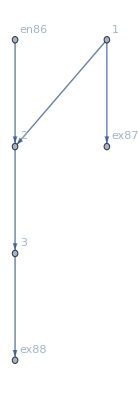

<|{1,1->2}→u506,{1,en479->1}→u506,{2,1->2}→-1+u506,{2,2->3}→u507,{2,2->4}→u508,{3,2->3}→-1+j484+u507,{3,3->ex480}→5,{4,2->4}→-j484+u508,{4,4->ex481}→1,{en479,en479->1}→u506,{ex480,3->ex480}→5,{ex481,4->ex481}→1|>

```mathematica
MFGEquations["FG"]
```

```mathematica
MFGEquations["criticalreduced1"][[2]](*//KeySort*)
```

<|j93→1,u115→0,u117→3,j89→0,j91→0,j92→0,j94→1,j95→0,j96→0,j97→0,j98→0,jt100→0,jt101→0,jt102→0,jt103→0,jt104→0,jt105→1,jt106→0,jt107→0,jt108→0,jt99→1,u110→0,u112→3,u114→1,u116→1,u118→1,j90→1,u109→0,u111→1,u113→1|>

#### Non-linear case

```mathematica
alpha = 0;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j89→0,j90→1.,j91→0.,j92→0.,j93→1,j94→1.,j95→0,j96→0,j97→0,j98→0,jt100→0,jt101→0,jt102→0,jt103→0,jt104→0,jt105→1.,jt106→0.,jt107→0.,jt108→0,jt99→1.,u109→0,u110→0,u111→0.705756,u112→3,u113→0.705756,u114→0.705756,u115→0,u116→0.705756,u117→3,u118→0.705756|>

```mathematica
alpha = 0.1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j89→0,j90→1.,j91→0.,j92→0.,j93→1,j94→1.,j95→0,j96→0,j97→0,j98→0,jt100→0,jt101→0,jt102→0,jt103→0,jt104→0,jt105→1.,jt106→0.,jt107→0.,jt108→0,jt99→1.,u109→0,u110→0,u111→0.72685,u112→3,u113→0.72685,u114→0.72685,u115→0,u116→0.72685,u117→3,u118→0.72685|>

```mathematica
alpha = 0.3;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is Min[0.116271 √(0.+Abs[-6.93911+1. j51-IntM[10-j51]]^2+Abs[3.06089-1. j51-IntM[j51]]^2),√(0.+Abs[-6.93911+1. j51-IntM[10-j51]]^2+Abs[3.06089-1. j51-IntM[j51]]^2),(√(0.+Abs[-6.93911+1. j51-IntM[10-j51]]^2+Abs[3.06089-1. j51-IntM[j51]]^2))/(√(55.232+Abs[10-j51+IntM[10-j51]]^2+Abs[j51+IntM[j51]]^2))]

ReplaceAll::reps: {u75==u76&&10-u74+u80==7.43182&&j51-u75+u81==j51+IntM[j51]&&10-j51-u76+u82==10-j51+IntM[10-j51]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

AssociateTo::invlb: The argument u75==u76&&10-u74+u80==7.43182&&j51-u75+u81==j51+IntM[j51]&&10-j51-u76+u82==10-j51+IntM[10-j51] is not a list, Rule, or Association.

ReplaceAll::reps: {u75==u76&&10-u74+u80==7.43182&&j51-u75+u81==j51+IntM[j51]&&10-j51-u76+u82==10-j51+IntM[10-j51]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

$Aborted

```mathematica
alpha = 0.9;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

```mathematica
alpha = 1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

```mathematica
alpha = 1.2;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

```mathematica
alpha = 1.5;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

```mathematica
alpha = 1.6;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,
SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

```mathematica
alpha = 1.8;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

```mathematica
alpha = 1.9;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

```mathematica
alpha = 2;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],20,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```